{{δ→InterpolatingFunction[…]}}

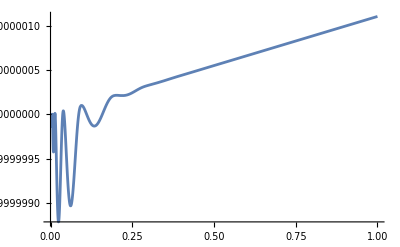

-Graphics-

```mathematica
OmegM=0.3;
OmegR=10^(-4);
H0=67;
k=10^(-3) H0;

eq=δ''[a]+(3/a-(3*OmegM/a+4*OmegR/a^2)/(2*(OmegM+OmegR/a))+(9*H0^2*(OmegM/a+OmegR/a^2))/(2*k^2)) δ'[a]-(3/(2*a)) δ[a]==0;

a0=10^-4;

(*Initial conditions at a0*)
ic={δ[a0]==1,δ'[a0]==0};

(*Numeric integration*)
sol1=NDSolve[{eq,ic},δ,{a,a0,1},Method->{"StiffnessSwitching","NonstiffTest"->False}]
Plot[Evaluate[δ[a]/. sol1],{a,a0,1}]
```

{{δ→InterpolatingFunction[…]}}

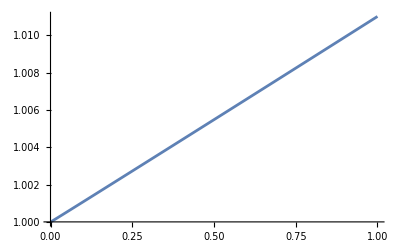

```mathematica
OmegM=0.3;
OmegR=10^(-4);
H0=67;
k=10^(-1) H0;

eq=δ''[a]+(3/a-(3*OmegM/a+4*OmegR/a^2)/(2*(OmegM+OmegR/a))+(9*H0^2*(OmegM/a+OmegR/a^2))/(2*k^2)) δ'[a]-(3/(2*a)) δ[a]==0;

a0=10^-4;

(*Initial conditions at a0*)
ic={δ[a0]==1,δ'[a0]==0};

(*Numeric integration*)
sol2=NDSolve[{eq,ic},δ,{a,a0,1},Method->{"StiffnessSwitching","NonstiffTest"->False}]
Plot[Evaluate[δ[a]/. sol2],{a,a0,1}]
```

{{δ→InterpolatingFunction[…]}}

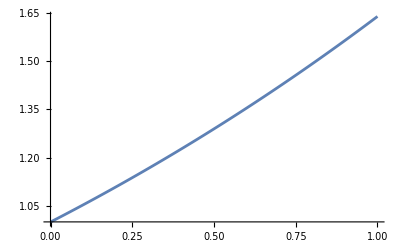

```mathematica
OmegM=0.3;
OmegR=10^(-4);
H0=67;
k= H0;

eq=δ''[a]+(3/a-(3*OmegM/a+4*OmegR/a^2)/(2*(OmegM+OmegR/a))+(9*H0^2*(OmegM/a+OmegR/a^2))/(2*k^2)) δ'[a]-(3/(2*a)) δ[a]==0;

a0=10^-4;

(*Initial conditions at a0*)
ic={δ[a0]==1,δ'[a0]==0};

(*Numeric integration*)
sol3=NDSolve[{eq,ic},δ,{a,a0,1},Method->{"StiffnessSwitching","NonstiffTest"->False}]
Plot[Evaluate[δ[a]/. sol3],{a,a0,1}]
```

{{δ→InterpolatingFunction[…]}}

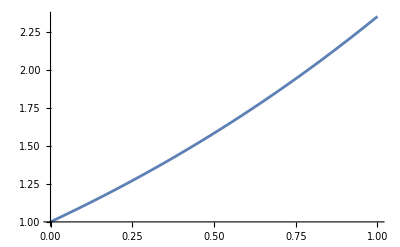

```mathematica
OmegM=0.3;
OmegR=10^(-4);
H0=67;
k= 100H0;

eq=δ''[a]+(3/a-(3*OmegM/a+4*OmegR/a^2)/(2*(OmegM+OmegR/a))+(9*H0^2*(OmegM/a+OmegR/a^2))/(2*k^2)) δ'[a]-(3/(2*a)) δ[a]==0;

a0=10^-4;

(*Initial conditions at a0*)
ic={δ[a0]==1,δ'[a0]==0};

(*Numeric integration*)
sol4=NDSolve[{eq,ic},δ,{a,a0,1},Method->{"StiffnessSwitching","NonstiffTest"->False}]
Plot[Evaluate[δ[a]/. sol4],{a,a0,1}]
```

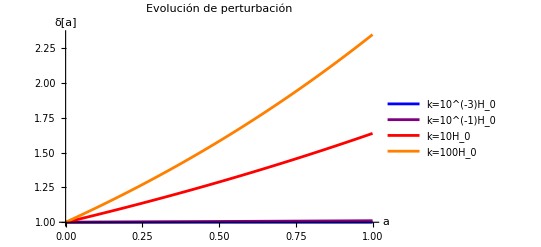

```mathematica
Plot1=Plot[Evaluate[δ[a]/. sol1],{a,a0,1},AxesLabel->{"a","δ[a]"},PlotLabel->"Evolución de perturbación",PlotLegends->{"k=10^(-3)H_0"},PlotStyle->Blue];
Plot2=Plot[Evaluate[δ[a]/. sol2],{a,a0,1},PlotLegends->{"k=10^(-1)H_0"},PlotStyle->Purple];
Plot3=Plot[Evaluate[δ[a]/. sol3],{a,a0,1},PlotLegends->{"k=10H_0"},PlotStyle->Red];
Plot4=Plot[Evaluate[δ[a]/. sol4],{a,a0,1},PlotLegends->{"k=100H_0"},PlotStyle->Orange];
Show[Plot1,Plot2,Plot3,Plot4,PlotRange->All]
```